# ParseWords 1.01

## documentation notebook

Eric Rowland
http://people.hofstra.edu/Eric_Rowland/packages.html

## Introduction

ParseWords is a package for studying parse words of pairs of binary trees under a certain grammar related to the four color theorem.
This introduction gets you started with a few features of the package; the next section provides a complete list of package symbols along with their usage messages and further examples.

ParseWords uses functions from my package BinaryTrees, so you will need to have BinaryTrees installed as well.

To use ParseWords, first you will need to load the package by evaluating the following cell.  (If you need help, see loading a package.)

```mathematica
<<ParseWords`
```

### Representing trees

A rooted tree is represented by an expression in which each vertex corresponds to a list containing its children.  For example, here is a 5-leaf binary tree:

```mathematica
{{{},{}},{{{},{}},{}}}
```

The Wolfram Language symbol TreeForm displays expressions graphically.  BareTreeForm uses TreeForm to draw trees without vertex labels:

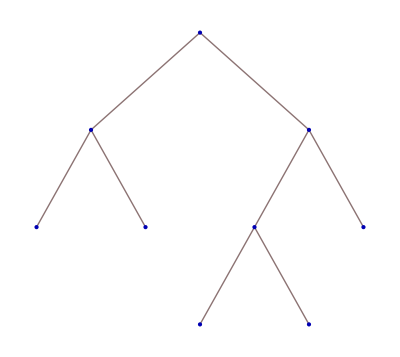

```mathematica
BareTreeForm[{{{},{}},{{{},{}},{}}}]
```

BinaryTrees gives a list of all binary trees with a fixed number of leaves.

{{{},{{},{{},{}}}},{{},{{{},{}},{}}},{{{},{}},{{},{}}},{{{},{{},{}}},{}},{{{{},{}},{}},{}}}

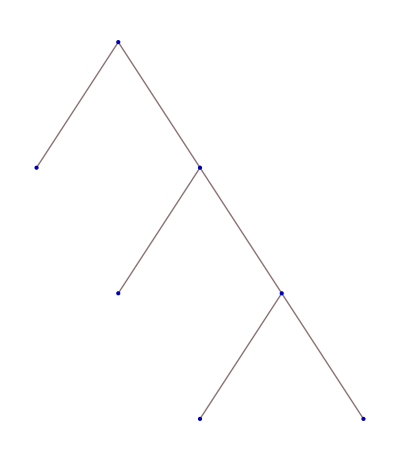
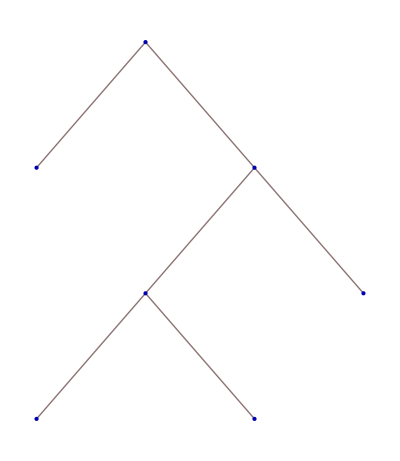
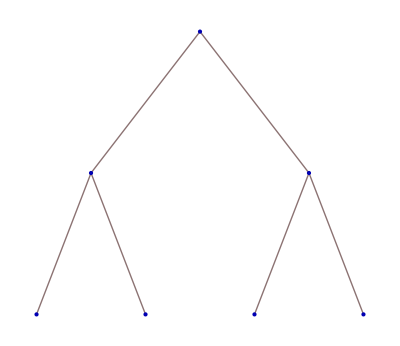
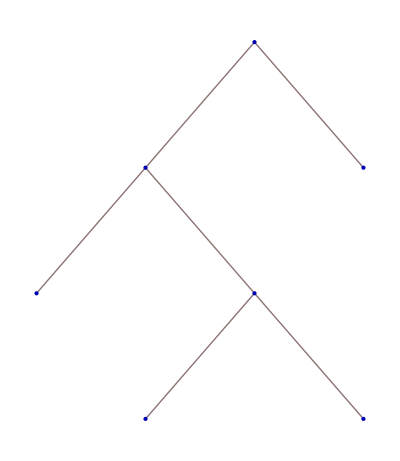
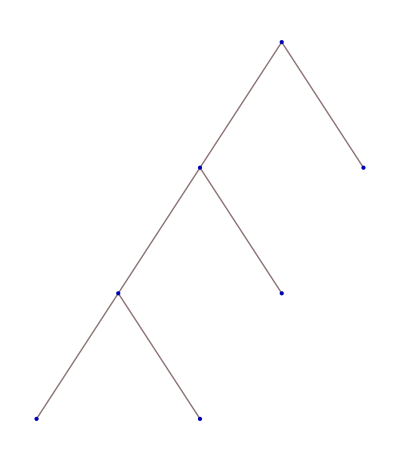

```mathematica
BinaryTrees[4]
BareTreeForm/@%
```

There are also a few parameterized families of trees supported.  These include left comb trees, crooked trees, and turn trees.

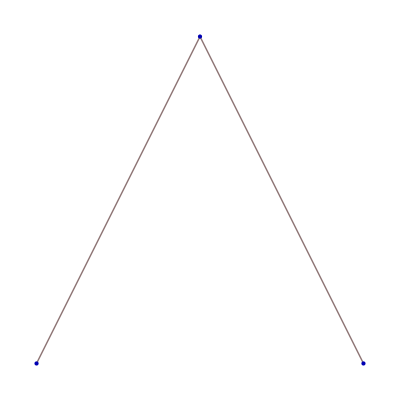
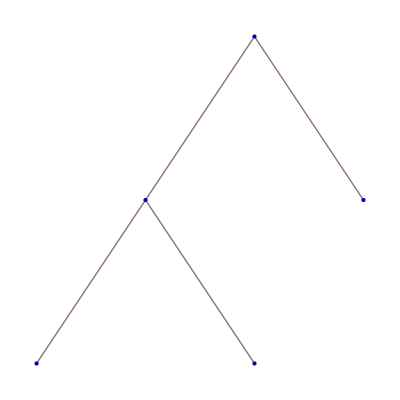
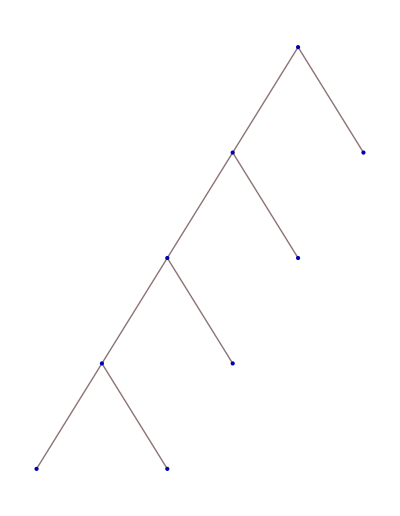
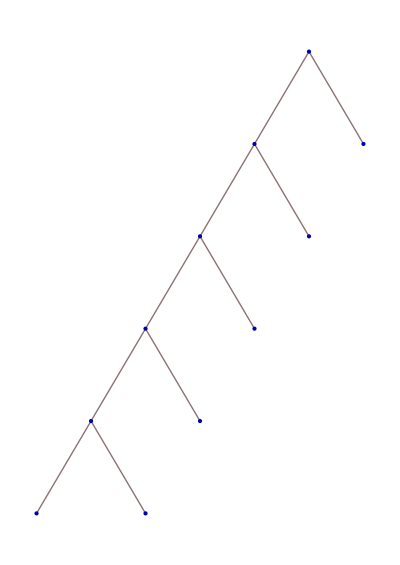
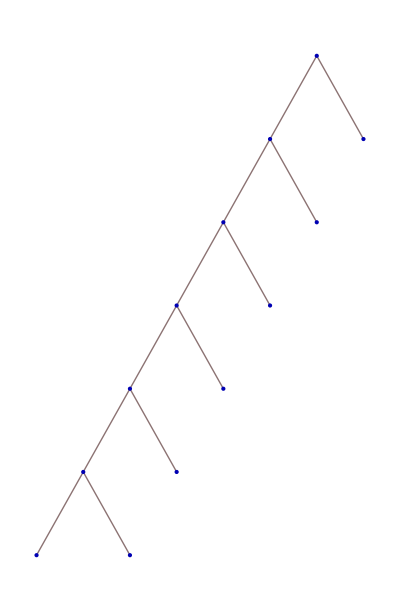
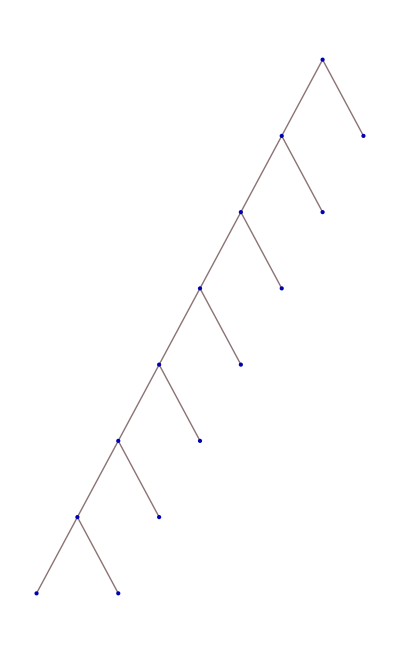
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[BareTreeForm[LeftCombTree[n]],{n,8}]
```

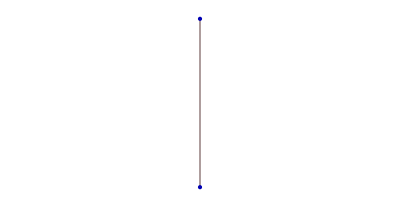
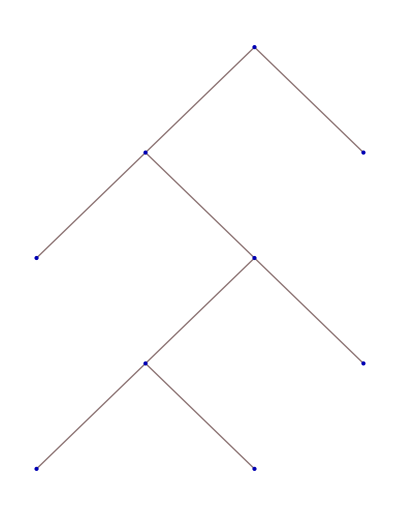
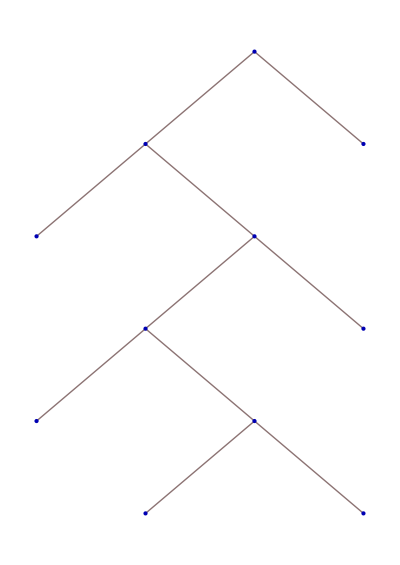
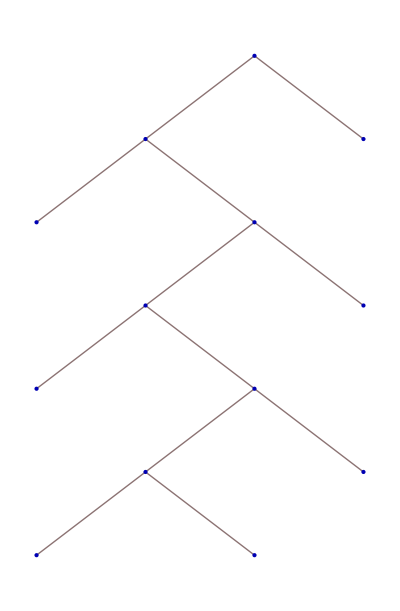
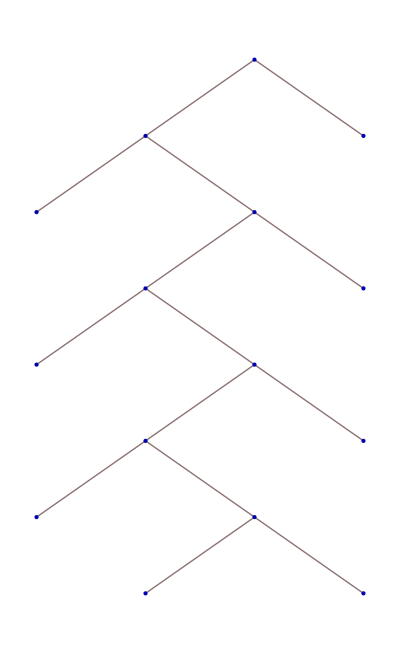
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[BareTreeForm[LeftCrookedTree[n]],{n,8}]
```

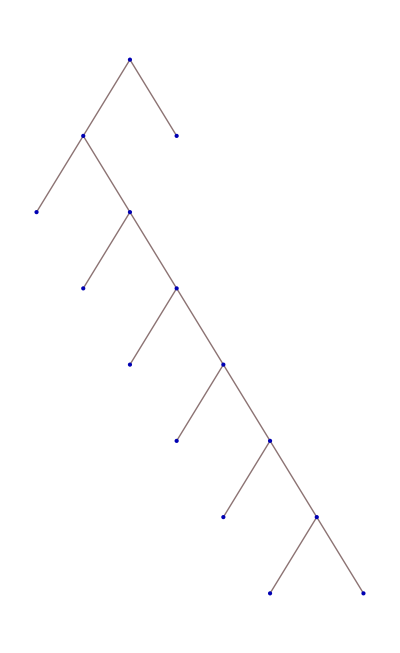
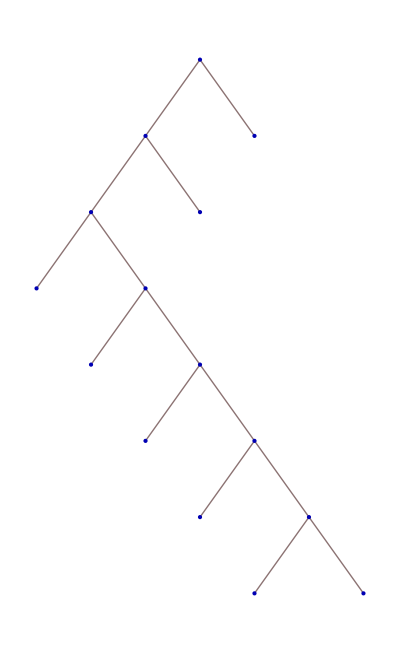
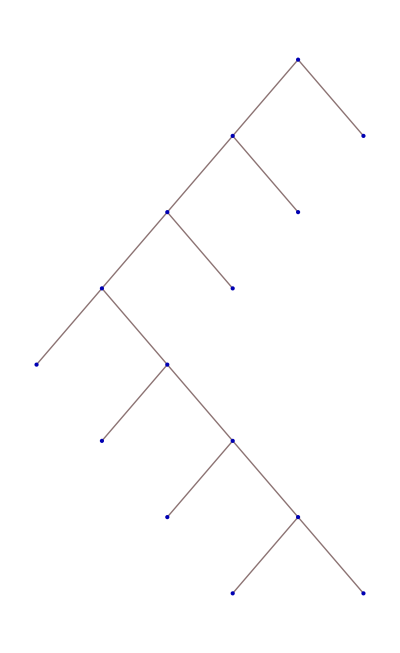
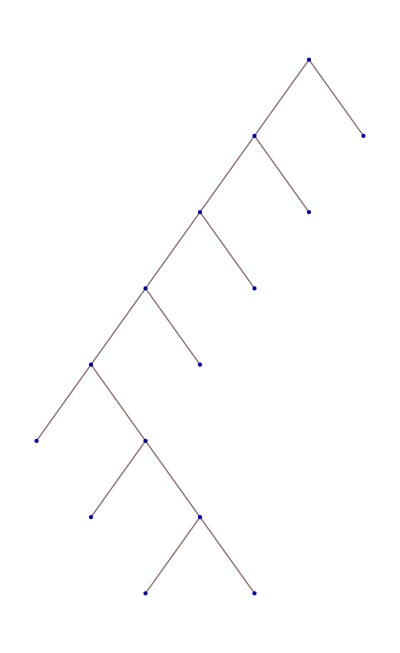
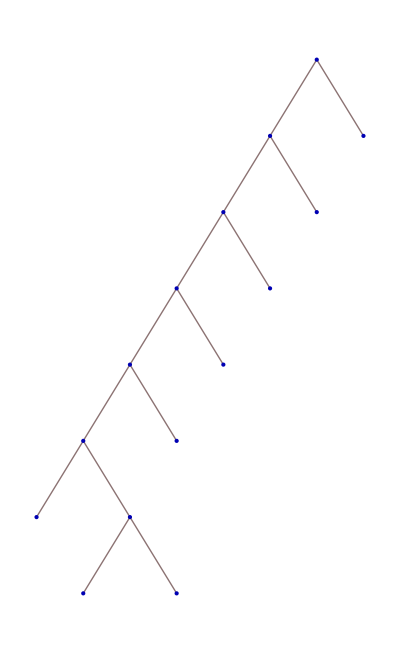
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[BareTreeForm[LeftTurnTree[n,8-n]],{n,6}]
```

### Parse words

A binary tree parses a ternary word w if there is a labeling of the vertices of the tree such that the leaves are labeled with the letters of w (left to right) and every -Graphics- structure in the tree contains all three letters.  For example, here is a labeling that shows that this 6-leaf tree parses 011121:

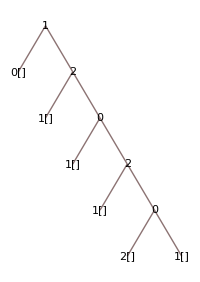

```mathematica
TreeForm[LabelTree[{{},{{},{{},{{},{{},{}}}}}},{0,1,1,1,2,1}],ImageSize->200]
```

ParseWords finds all the parse words of a tree (up to permutations of the alphabet).

```mathematica
ParseWords[{{},{{},{{},{{},{{},{}}}}}}]
```

{{0,0,0,0,0,1},{0,0,0,0,1,0},{0,0,0,1,1,2},{0,0,0,1,2,1},{0,0,1,1,0,1},{0,0,1,1,1,0},{0,0,1,2,0,2},{0,0,1,2,2,0},{0,1,1,0,0,2},{0,1,1,0,2,0},{0,1,1,1,1,2},{0,1,1,1,2,1},{0,1,2,0,0,1},{0,1,2,0,1,0},{0,1,2,2,1,2},{0,1,2,2,2,1}}

The four color theorem is equivalent to the statement that every pair of binary trees with the same number of leaves parse a common word.  When given multiple arguments, ParseWords finds the common parse words of several trees.

```mathematica
ParseWords[{{},{{},{{},{{},{{},{}}}}}},{{{},{}},{{{{},{}},{}},{}}}]
```

{{0,1,1,0,0,2},{0,1,2,0,0,1}}

For some parameterized families of trees, the parse words can be written explicitly:

```mathematica
Table[ParseWords[LeftCombTree[n],RightCombTree[n]],{n,8}]
```

{{{0}},{{0,1}},{{0,1,0}},{{0,1,1,2}},{{0,1,1,1,0}},{{0,1,1,1,1,2}},{{0,1,1,1,1,1,0}},{{0,1,1,1,1,1,1,2}}}

```mathematica
Table[ParseWords[LeftCombTree[n],RightCrookedTree[n]],{n,2,8}]
```

{{{0,1}},{{0,1,0}},{{0,1,0,0}},{{0,1,1,2,0}},{{0,1,0,2,2,0}},{{0,1,0,0,1,2,0}},{{0,1,0,2,1,1,2,0}}}

## Package symbols

#### AllParseWords

```mathematica
?AllParseWords
```

RowBox[List["AllParseWords", "[", StyleBox["tree", "TI"], "]"]] gives the list of words that are parsed by a binary tree.

```mathematica
AllParseWords[{{},{{},{{{},{}},{}}}}]
```

{{0,0,0,1,0},{0,0,0,2,0},{0,0,1,0,0},{0,0,1,2,1},{0,0,1,2,2},{0,0,2,0,0},{0,0,2,1,1},{0,0,2,1,2},{0,1,0,1,1},{0,1,0,2,2},{0,1,1,0,1},{0,1,2,0,2},{0,2,0,1,1},{0,2,0,2,2},{0,2,1,0,1},{0,2,2,0,2},{1,0,0,1,0},{1,0,1,0,0},{1,0,1,2,2},{1,0,2,1,2},{1,1,0,1,1},{1,1,0,2,0},{1,1,0,2,2},{1,1,1,0,1},{1,1,1,2,1},{1,1,2,0,0},{1,1,2,0,2},{1,1,2,1,1},{1,2,0,1,0},{1,2,1,0,0},{1,2,1,2,2},{1,2,2,1,2},{2,0,0,2,0},{2,0,1,2,1},{2,0,2,0,0},{2,0,2,1,1},{2,1,0,2,0},{2,1,1,2,1},{2,1,2,0,0},{2,1,2,1,1},{2,2,0,1,0},{2,2,0,1,1},{2,2,0,2,2},{2,2,1,0,0},{2,2,1,0,1},{2,2,1,2,2},{2,2,2,0,2},{2,2,2,1,2}}

#### BottomLeafDisjointQ

```mathematica
?BottomLeafDisjointQ
```

RowBox[List["BottomLeafDisjointQ", "[", RowBox[List[SubscriptBox[StyleBox["tree", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["tree", "TI"], StyleBox["2", "TR"]]]], "]"]] yields True if the path trees SubscriptBox[StyleBox["tree", "TI"], StyleBox["1", "TR"]] and SubscriptBox[StyleBox["tree", "TI"], StyleBox["2", "TR"]] share no bottom leaves, and False otherwise.

```mathematica
BottomLeafDisjointQ[{{},{{},{{},{}}}},{{{{},{}},{}},{}}]
```

True

#### BottomLeafLabels

```mathematica
?BottomLeafLabels
```

RowBox[List["BottomLeafLabels", "[", RowBox[List[StyleBox["tree", "TI"], ",", StyleBox["word", "TI"]]], "]"]] gives the labels received by the two bottom leaves of a path tree when the leaves are labeled with entries from StyleBox["word", "TI"].

```mathematica
BottomLeafLabels[{{},{{},{{{},{}},{}}}},{0,0,0,2,0}]
```

{0,2}

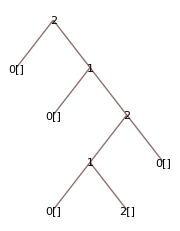

```mathematica
TreeForm[LabelTree[{{},{{},{{{},{}},{}}}},{0,0,0,2,0}],ImageSize->180]
```

#### CanonicalWord

```mathematica
?CanonicalWord
```

RowBox[List["CanonicalWord", "[", StyleBox["word", "TI"], "]"]] gives the lexicographically first word equivalent to StyleBox["word", "TI"] under permutations of the alphabet.

```mathematica
CanonicalWord[{2,0,0,1}]
```

{0,1,1,2}

#### ConsecutiveLeafPairs

```mathematica
?ConsecutiveLeafPairs
```

RowBox[List["ConsecutiveLeafPairs", "[", RowBox[List[SubscriptBox[StyleBox["tree", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["tree", "TI"], StyleBox["2", "TR"]]]], "]"]] gives the indices of all pairs of leaves that appear consecutively in a comb structure in two binary trees SubscriptBox[StyleBox["tree", "TI"], StyleBox["1", "TR"]] and SubscriptBox[StyleBox["tree", "TI"], StyleBox["2", "TR"]].

```mathematica
ConsecutiveLeafPairs[{{},{{},{{},{}}}},{{{{},{}},{}},{}}]
```

{{2,3}}

#### DecomposeTrees

```mathematica
?DecomposeTrees
```

RowBox[List["DecomposeTrees", "[", RowBox[List[SubscriptBox[StyleBox["tree", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["tree", "TI"], StyleBox["2", "TR"]]]], "]"]] gives all levels where partitioning the path trees SubscriptBox[StyleBox["tree", "TI"], StyleBox["1", "TR"]] and SubscriptBox[StyleBox["tree", "TI"], StyleBox["2", "TR"]] at that level creates the same partition of leaves in both trees.

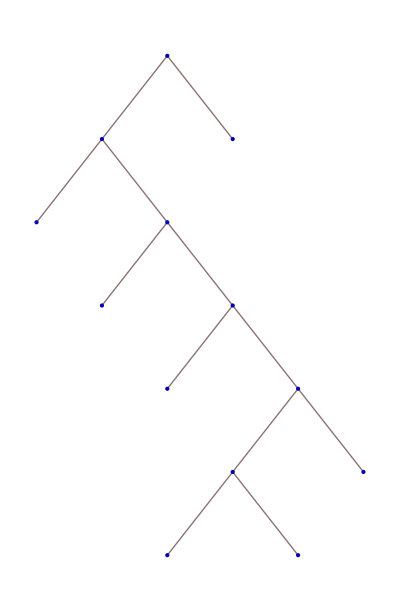
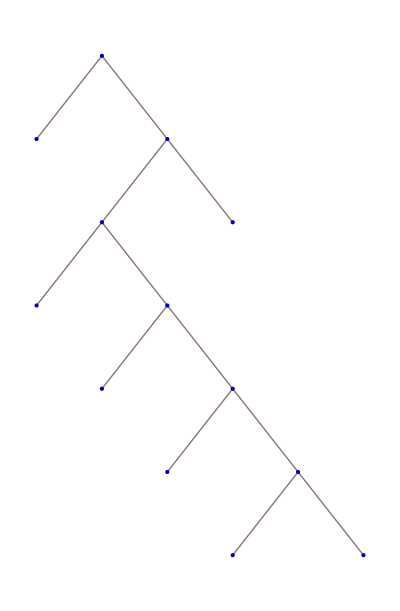

```mathematica
BareTreeForm/@{{{{},{{},{{},{{{},{}},{}}}}},{}},{{},{{{},{{},{{},{{},{}}}}},{}}}}
```

```mathematica
DecomposeTrees[{{{},{{},{{},{{{},{}},{}}}}},{}},{{},{{{},{{},{{},{{},{}}}}},{}}}]
```

{0,2,3,4}

#### IndecomposableQ

```mathematica
?IndecomposableQ
```

RowBox[List["IndecomposableQ", "[", RowBox[List[SubscriptBox[StyleBox["tree", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["tree", "TI"], StyleBox["2", "TR"]]]], "]"]] yields True if the path trees SubscriptBox[StyleBox["tree", "TI"], StyleBox["1", "TR"]] and SubscriptBox[StyleBox["tree", "TI"], StyleBox["2", "TR"]] are indecomposable, and False otherwise.

```mathematica
IndecomposableQ[{{{},{{},{{},{{{},{}},{}}}}},{}},{{},{{{},{{},{{},{{},{}}}}},{}}}]
```

False

#### LabelLeaves

```mathematica
?LabelLeaves
```

RowBox[List["LabelLeaves", "[", RowBox[List[StyleBox["tree", "TI"], ",", StyleBox["word", "TI"]]], "]"]] labels the leaves of a binary tree with entries from StyleBox["word", "TI"].

```mathematica
LabelLeaves[{{},{{},{{{},{}},{}}}},{0,0,0,2,0}]
```

{0,{0,{{0,2},0}}}

#### LabelTree

```mathematica
?LabelTree
```

RowBox[List["LabelTree", "[", RowBox[List[StyleBox["tree", "TI"], ",", StyleBox["word", "TI"]]], "]"]] labels the vertices of a binary tree with labels induced by a parse word.

```mathematica
LabelTree[{{},{{},{{{},{}},{}}}},{0,0,0,2,0}]
```

2[0[],1[0[],2[1[0[],2[]],0[]]]]

```mathematica
TreeForm[%,ImageSize->180]
```

-Graphics-

#### MutuallyCrookedQ

```mathematica
?MutuallyCrookedQ
```

RowBox[List["MutuallyCrookedQ", "[", RowBox[List[SubscriptBox[StyleBox["tree", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["tree", "TI"], StyleBox["2", "TR"]]]], "]"]] yields True if the binary trees SubscriptBox[StyleBox["tree", "TI"], StyleBox["1", "TR"]] and SubscriptBox[StyleBox["tree", "TI"], StyleBox["2", "TR"]] are mutually crooked, and False otherwise.

```mathematica
MutuallyCrookedQ[{{},{{},{}}},{{{},{}},{}}]
```

True

Find the pairs of 4-leaf binary trees that are mutually crooked:

```mathematica
(BareTreeForm/@#1&)/@Select[Subsets[BinaryTrees[4],{2}],MutuallyCrookedQ@@#1&]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

#### ParentLabel

```mathematica
?ParentLabel
```

RowBox[List["ParentLabel", "[", RowBox[List[StyleBox["tree", "TI"], ",", StyleBox["word", "TI"], ",", StyleBox["i", "TI"]]], "]"]] gives the label received by the parent of the StyleBox["i", "TI"]th leaf when the leaves are labeled with StyleBox["word", "TI"].

```mathematica
ParentLabel[{{},{{},{{{},{}},{}}}},{0,0,0,2,0},4]
```

1

```mathematica
TreeForm[LabelTree[{{},{{},{{{},{}},{}}}},{0,0,0,2,0}],ImageSize->180]
```

-Graphics-

#### ParseWords

```mathematica
?ParseWords
```

RowBox[List["ParseWords", "[", StyleBox["tree", "TI"], "]"]] gives the list of words parsed by a tree that are lexicographically first in their equivalent classes (under permutations of RowBox[List["{", RowBox[List[StyleBox["0", "TR"], ",", StyleBox["1", "TR"], ",", StyleBox["2", "TR"]]], "}"]]).
RowBox[List["ParseWords", "[", RowBox[List[SubscriptBox[StyleBox["tree", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["tree", "TI"], StyleBox["2", "TR"]], ",", StyleBox["\[Ellipsis]", "TR"]]], "]"]] gives the lexicographically first words that are simultaneously parsed by several trees.

```mathematica
ParseWords[{{},{{},{{{},{}},{}}}}]
```

{{0,0,0,1,0},{0,0,1,0,0},{0,0,1,2,1},{0,0,1,2,2},{0,1,0,1,1},{0,1,0,2,2},{0,1,1,0,1},{0,1,2,0,2}}

```mathematica
Union[CanonicalWord/@AllParseWords[{{},{{},{{{},{}},{}}}}]]
```

{{0,0,0,1,0},{0,0,1,0,0},{0,0,1,2,1},{0,0,1,2,2},{0,1,0,1,1},{0,1,0,2,2},{0,1,1,0,1},{0,1,2,0,2}}

Find the common parse words of a tree and its left–right reflection:

```mathematica
ParseWords[{{},{{},{{{},{}},{}}}},{{{{},{{},{}}},{}},{}}]
```

{{0,0,1,0,0},{0,0,1,2,1},{0,0,1,2,2},{0,1,0,2,2}}

#### RootLabel

```mathematica
?RootLabel
```

RowBox[List["RootLabel", "[", RowBox[List[StyleBox["tree", "TI"], ",", StyleBox["word", "TI"]]], "]"]] gives the label received by the root of a binary tree when the leaves are labeled with entries from StyleBox["word", "TI"].

```mathematica
RootLabel[{{},{{},{{{},{}},{}}}},{0,0,0,2,0}]
```

2

The label of the root is an invariant of the word:

```mathematica
DeleteCases[RootLabel[#,{0,1,2,0,2}]&/@BinaryTrees[5],_RootLabel]
```

{1,1,1,1,1,1}

#### SiblingLabel

```mathematica
?SiblingLabel
```

RowBox[List["SiblingLabel", "[", RowBox[List[StyleBox["tree", "TI"], ",", StyleBox["word", "TI"], ",", StyleBox["i", "TI"]]], "]"]] gives the label received by the sibling of the StyleBox["i", "TI"]th leaf when the leaves are labeled with StyleBox["word", "TI"].

```mathematica
SiblingLabel[{{},{{},{{{},{}},{}}}},{0,0,0,2,0},4]
```

0

```mathematica
TreeForm[LabelTree[{{},{{},{{{},{}},{}}}},{0,0,0,2,0}],ImageSize->180]
```

-Graphics-

#### WeaklyMutuallyCrookedQ

```mathematica
?WeaklyMutuallyCrookedQ
```

RowBox[List["WeaklyMutuallyCrookedQ", "[", RowBox[List[SubscriptBox[StyleBox["tree", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["tree", "TI"], StyleBox["2", "TR"]]]], "]"]] yields True if the path trees SubscriptBox[StyleBox["tree", "TI"], StyleBox["1", "TR"]] and SubscriptBox[StyleBox["tree", "TI"], StyleBox["2", "TR"]] are weakly mutually crooked, and False otherwise.

These two trees are weakly mutually crooked but not mutually crooked:

```mathematica
BareTreeForm/@{{{},{{},{{},{}}}},{{{{},{}},{}},{}}}
```

{-Graphics-,-Graphics-}

```mathematica
WeaklyMutuallyCrookedQ[{{},{{},{{},{}}}},{{{{},{}},{}},{}}]
```

True

```mathematica
MutuallyCrookedQ[{{},{{},{{},{}}}},{{{{},{}},{}},{}}]
```

False

Find the pairs of 4-leaf path trees that are mutually crooked:

```mathematica
(BareTreeForm/@#1&)/@Select[Subsets[PathTrees[4],{2}],WeaklyMutuallyCrookedQ@@#1&]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}